```mathematica
NestList[f, x, 4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
RecurrenceTable[]
```

```mathematica
points = RandomReal[1, {10000,2}];
```

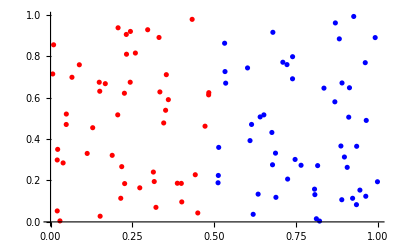

```mathematica
ListPlot[{Select[points, #[[1]]<0.5&], Select[points, #[[1]]>0.5&]}, PlotStyle->{Red, Blue}]
```

```mathematica
crit[x_]:=Norm[x-{0.5,0.5}]<0.2
```

```mathematica
critN[x_]:=Norm[x-{0.5,0.5}]>0.2
```

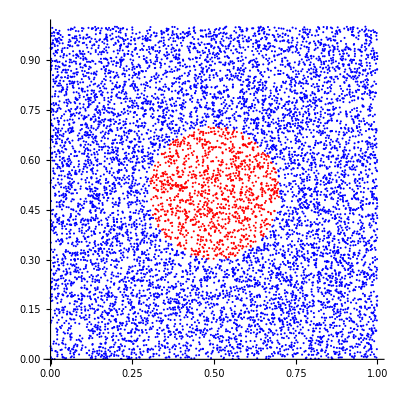

```mathematica
ListPlot[{Select[points, crit], Select[points, critN]}, PlotStyle->{Red, Blue}, AspectRatio->1]
```

```mathematica
(*Задача 1*)
```

```mathematica
RANDU[0] = 51
```

51

```mathematica
RANDU[n_]:=RANDU[n]=Mod[65539*RANDU[n-1],2^31]
```

```mathematica
list = {51}
```

{51}

```mathematica
Do[AppendTo[list, RANDU[i]],{i, 1, 2000}]
```

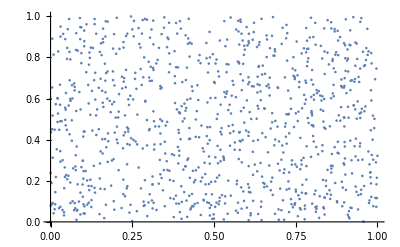

```mathematica
ListPlot[Partition[list/2^31,2]]
```

```mathematica
list2 = {47}
```

{47}

```mathematica
Do[AppendTo[list2, RANDU[i]],{i, 1, 30000}]
```

```mathematica
ListPointPlot3D[Partition[list2/2^31,3]]
```

-Graphics3D-

```mathematica
(*Задача 2*)
```

```mathematica
SeedRandom[12345, Method->"MersenneTwister"]
```

```mathematica
list3 = RandomReal[1, {10000, 3}];
```

```mathematica
ListPointPlot3D[list3]
```

-Graphics3D-

```mathematica
(*генерирует не полосочки*)
```

```mathematica
(*Геометрический метод Монте-Карло*)
```

```mathematica
(*Задача 3*)
```

```mathematica
points3 = RandomReal[{-2,2}, {1000,2}];
```

```mathematica
crit3[x_]:=Norm[x-{0,0}]<2
```

```mathematica
critN3[x_]:=Norm[x-{0,0}]>2
```

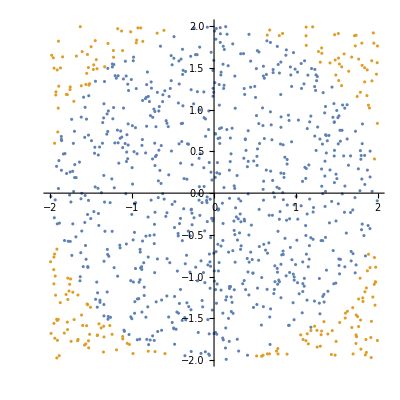

```mathematica
ListPlot[{Select[points3, crit3], Select[points3, critN3]}, AspectRatio->1]
```

```mathematica
k3=Length[Select[points3, crit3]]
```

776

```mathematica
n3 = Length[points3]
```

1000

```mathematica
s3 = 16
```

16

```mathematica
S3 = s3*(k3/n3)//N
```

12.416

```mathematica
π*4//N
```

12.5664

```mathematica
(*площадь фигуры по формуле 12.416, это похоже на правду*)
```

```mathematica
(*Задача 4*)
```

```mathematica
list4 = {}
```

{}

```mathematica
Do[
points4 = RandomReal[{-1,1}, {100,2}];
crit4[x_]:=Norm[x-{0,0}]<1;
critN4[x_]:=Norm[x-{0,0}]>1;
k4=Length[Select[points4, crit4]];
n4=Length[points4];
s4 = 4;
S4 = s4*(k4/n4)//N;
AppendTo[list4, S4], {i, 1, 100}]
```

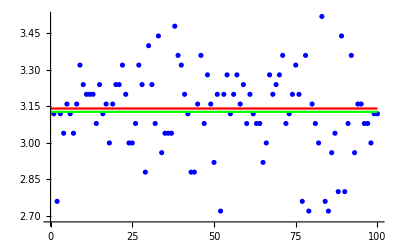

```mathematica
Show[ListPlot[list4, PlotStyle->Blue], Plot[π,{x, 0, 100}, PlotStyle->Red], Plot[Mean[list4],{x, 0, 100}, PlotStyle->Green]]
```

```mathematica
Variance[list4]
```

0.0296727

```mathematica
(*Точное значение довольно близко к настоящему значению пи, дисперсия равна 0.029672727272727267*)
```

```mathematica
(*Задача 5*)
```

```mathematica
list51={}
```

{}

```mathematica
Do[
points51 = RandomReal[{-1,1}, {100,2}];
crit4[x_]:=Norm[x-{0,0}]<1;
critN4[x_]:=Norm[x-{0,0}]>1;
k4=Length[Select[points51, crit4]];
n4=Length[points51];
s4 = 4;
S4 = s4*(k4/n4)//N;
AppendTo[list51, S4], {i, 1, 200}]
```

```mathematica
list52 = {}
```

{}

```mathematica
Do[
points52 = RandomReal[{-1,1}, {1000,2}];
crit4[x_]:=Norm[x-{0,0}]<1;
critN4[x_]:=Norm[x-{0,0}]>1;
k4=Length[Select[points52, crit4]];
n4=Length[points52];
s4 = 4;
S4 = s4*(k4/n4)//N;
AppendTo[list52, S4], {i, 1, 200}]
```

```mathematica
list53 = {}
```

{}

```mathematica
Do[
points53 = RandomReal[{-1,1}, {5000,2}];
crit4[x_]:=Norm[x-{0,0}]<1;
critN4[x_]:=Norm[x-{0,0}]>1;
k4=Length[Select[points53 ,crit4]];
n4=Length[points53];
s4 = 4;
S4 = s4*(k4/n4)//N;
AppendTo[list53, S4], {i, 1, 200}]
```

```mathematica
list54 = {}
```

{}

```mathematica
Do[
points54 = RandomReal[{-1,1}, {10000,2}];
crit4[x_]:=Norm[x-{0,0}]<1;
critN4[x_]:=Norm[x-{0,0}]>1;
k4=Length[Select[points54, crit4]];
n4=Length[points54];
s4 = 4;
S4 = s4*(k4/n4)//N;
AppendTo[list54, S4], {i, 1, 200}]
```

```mathematica
m51 = Mean[list51]
```

3.1482

```mathematica
s51 = StandardDeviation[list51]
```

0.147872

```mathematica
(*для 10 точек среднее значение 3.1482 и стандартное отклонение 0.14787187174125202*)
```

```mathematica
m52= Mean[list52]
```

3.14106

```mathematica
s52 = StandardDeviation[list52]
```

0.0496735

```mathematica
(*для 1000 точек среднее значение 3.14106 и стандартное отклонение 0.049673470468064855*)
```

```mathematica
m53 = Mean[list53]
```

3.14155

```mathematica
s53=StandardDeviation[list53]
```

0.0233326

```mathematica
(*для 5000 точек среднее значение 3.1415480000000002 и стандартное отклонение 0.02333264144463544*)
```

```mathematica
m54 = Mean[list54]
```

3.14173

```mathematica
s54 = StandardDeviation[list54]
```

0.0165656

```mathematica
(*для 10000 точек среднее значение 3.141728 и стандартное отклонение 0.016565618448245882*)
```

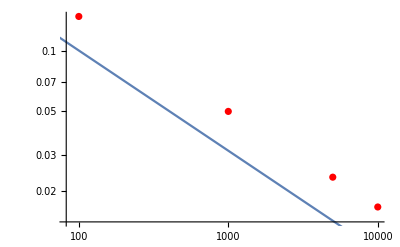

```mathematica
Show[ListLogLogPlot[{{100, s51}, {1000, s52}, {5000, s53}, {10000, s54}}, PlotStyle->Red], LogLogPlot[1/Sqrt[x], {x, 0, 10^4}]]
```

```mathematica
(*график зависимости стандартного отклонения от количества точек - оно уменьшается с увеличением числа точек*)
```

```mathematica
(*Задача 6*)
```

```mathematica
vHS[num_]:=Module[{points,center, crit, k, n,s,V},
points= RandomReal[{-1,1}, {10000,num}];
center = {};
Do[AppendTo[center, 0],{i, 1, num}];
crit[x_]:=Norm[x-center]<1;
k=Length[Select[points, crit]];
n=Length[points];
s= 2^num;
V = s*(k/n)//N;
Return[V]
]
```

```mathematica
(*функция создает массив н-мерных точек, н-мерный центр, методом Монте-Карло рассчитывает для него объем*)
```

```mathematica
listPoints = {}
```

{}

```mathematica
Do[AppendTo[listPoints,{i, vHS[i]}], {i, 1, 10}]
```

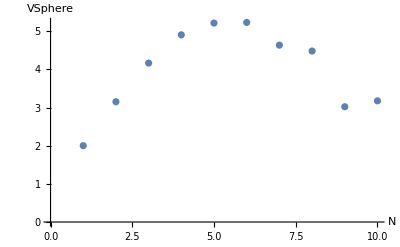

```mathematica
ListPlot[listPoints,AxesLabel->{"N", "VSphere"}]
```

```mathematica
(*объем возрастает до 5мерного пространства, а потом убывает, выглядит пугающе*)
```

```mathematica
(*Задача 7*)
```

```mathematica
vHR[num_]:=Module[{points,center, crit, k, n,s,V},
points= RandomReal[{-1,1}, {10000,num}];
center = {};
Do[AppendTo[center, 0],{i, 1, num}];
crit[x_]:=Norm[x-center]<1 &&Norm[x-center]>0.9;
k=Length[Select[points, crit]];
n=Length[points];
s= 2^num;
V = s*(k/n)//N;
Return[V]
]
```

```mathematica
listD = {}
```

{}

```mathematica
Do[AppendTo[listD,{i, vHR[i]/vHS[i]}], {i, 2, 10}]
```

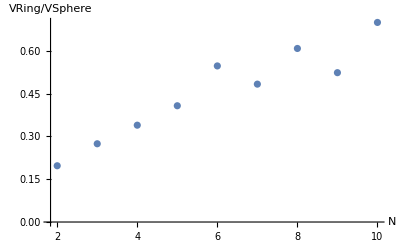

```mathematica
ListPlot[listD, AxesLabel->{"N", "VRing/VSphere"}]
```

```mathematica
(*отношение объема выглядит несколько странно, сначала оно довольно равномерно увеличивается, зачем есть серия из трех пиков и двух падений, в целом увеличивается с увеличением н*)
```